```mathematica
(* Setup and housekeeping stuff *)
ClearAll["Global`*"];
If[Length[$FrontEnd] > 0,NBDir=SetDirectory[NotebookDirectory[]]];(* If running from the Notebook interface *)
rootDir = SetDirectory["../../.."];(* root directory below which all code resides *)
CoreCodeDir=SetDirectory[rootDir<>"/Mathematica/CoreCode"];
MainCodeDir=SetDirectory[rootDir<>"/Mathematica/Examples/Handout"];
FigsDir=SetDirectory[MainCodeDir<>"/Figures"];
Get[CoreCodeDir<>"/FriedmanPIH-Setup.m"];(* Setup stuff, for creating figures etc *)
Get[CoreCodeDir<>"/FriedmanPIH-TimeSeries.m"];(* Further setup stuff, for creating figures etc *)
```

```mathematica
SetupForSims; (* Create empty dataset *)
𝔊=1.01; (* Growth factor *)
ϑstd=0.02; (* Standard deviation of transitory shock *)

Do[AddObs,{NObs=50}]; (* Add 50 observations to the dataset *)
```

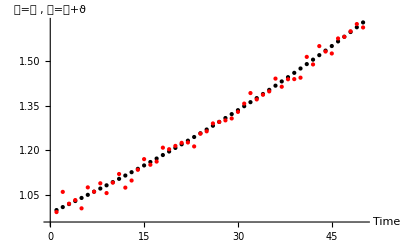

```mathematica
𝒸Color=Black;
𝒸Plot=ListPlot[Transpose[{ObsList,𝒸}],PlotStyle->𝒸Color];
𝓎Color=Red;
𝓎Plot=ListPlot[Transpose[{ObsList,𝓎}],PlotStyle->𝓎Color];
𝒸𝓎VsTimePlot=Show[𝒸Plot,𝓎Plot,AxesLabel->{"Time","𝒸=𝓅 , 𝓎=𝓅+ϑ"}];
ExportFigure[𝒸𝓎VsTimePlot,"CYVsTimePlot"]
(* Time series plot of 50 years of data *)
```

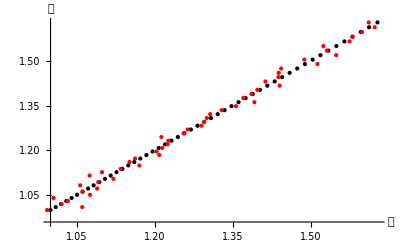

```mathematica
𝒸eq𝓅Color=Black;
𝒸eq𝓅Plot=ListPlot[Transpose[{𝓅,𝒸}],PlotStyle->𝒸eq𝓅Color];
𝓎PIHPlot=ListPlot[Transpose[{𝓎,𝓅}],PlotStyle->𝓎Color];
𝒸tvs𝓎tPlot=Show[𝒸eq𝓅Plot,𝓎PIHPlot,AxesLabel->{"𝓎","𝒸"}];
Print[ExportFigure[𝒸tvs𝓎tPlot,"CtvsYtPlot"]];
```

```mathematica
(* Estimation of Keynesian model on annual time series data *)
Print[FitLine=LinearModelFit[Transpose[{𝓎,𝒸}],{1,y},y]];
```

FittedModel[0.00680815+0.995575 y]

```mathematica
Δ𝓎=Take[𝓎,-(NObs-1)]-Take[𝓎,(NObs-1)];
Δ𝒸=Take[𝒸,-(NObs-1)]-Take[𝒸,(NObs-1)];

(* Estimation of Keynesian model on annual first-differenced data *)
Print[FitLine=LinearModelFit[Transpose[{Δ𝓎,Δ𝒸}],{ΔY},ΔY]];
```

FittedModel[0.0127946+0.00228556 ΔY]

```mathematica
SetupForSims;
𝔊=1.0;
𝓅Std=0.05;
ϑStd=0.05;
AddObsToTranShk:=AppendTo[ϑ,RandomReal[NormalDistribution[0,ϑStd]]];
AddObsToPermLev:=AppendTo[𝓅, 1+RandomReal[NormalDistribution[0,𝓅Std]]];
Do[AddObs,{NObs=200}];
Print[FitLine2=LinearModelFit[Transpose[{𝓎,𝒸}],{1,y},y]];
Print["Predicted coefficient from Friedman formula:",(𝓅Std)^2/((𝓅Std)^2+(ϑStd)^2)];
FitPlot2=Plot[FitLine2[y],{y,Min[𝓎],Max[𝓎]},PlotStyle->Red];
𝓎Color=Red;
𝓎PIHPlot2=ListPlot[Transpose[{𝓎,𝒸}],PlotStyle->𝓎Color];
Degree45=Plot[𝓅,{𝓅,0,1.5},PlotStyle->Black];
```

FittedModel[0.493009+0.508719 y]

Predicted coefficient from Friedman formula:0.5

FittedModel[0.107549+0.905834 y]

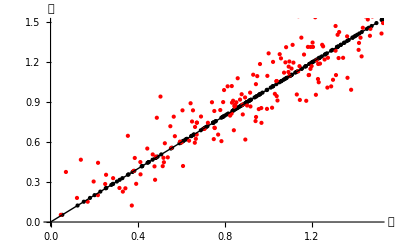

```mathematica
SetupForSims;
Group= GroupFarmer=3;
AddObsToTranShk:=AppendTo[ϑ,RandomReal[NormalDistribution[0,ϑStd GroupFarmer]]];
AddObsToPermLev:=AppendTo[𝓅, 1+RandomReal[NormalDistribution[0,10𝓅Std]]];

Do[AddObs,{NObs}];
Print[FitLine=LinearModelFit[Transpose[{𝓎,𝒸}],{1,y},y]];FitPlot=Plot[FitLine,{y,Min[𝓎],Max[𝓎]},PlotStyle->Black];
Degree45=Plot[y,{y,0,1.5},PlotStyle->Black];
𝒸eq𝓅Color=Black;
𝒸eq𝓅Plot=ListPlot[Transpose[{𝓅,𝒸}],PlotStyle->𝒸eq𝓅Color];
𝓎PIHPlot=ListPlot[Transpose[{𝓎,𝓅}],PlotStyle->𝓎Color];
𝒸iVs𝓎iPlot=Show[𝒸eq𝓅Plot,𝓎PIHPlot,AxesLabel->{"𝓎","𝒸"}];
𝒸iVs𝓎iVsFitOneGroupPlot=Show[𝒸iVs𝓎iPlot,FitPlot,Degree45,PlotRange->{{0,1.5},{0,1.5}},AxesOrigin->{0.,0.}];
Print[ExportFigure[𝒸iVs𝓎iVsFitOneGroupPlot,"CiVsYiVsFitOneGroupPlotv3"]];
```

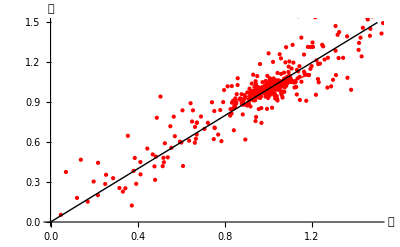

```mathematica
𝒸iVs𝓎iPlot=Show[𝓎PIHPlot2,𝓎PIHPlot,AxesLabel->{"𝓎","𝒸"},PlotRange->{{1-3 ϑStd  ,1+3 ϑStd  },Automatic}];𝒸iVs𝓎iVsFitAllPlot=Show[𝒸iVs𝓎iPlot,FitPlot2,FitPlot,Degree45
,PlotRange->{{0.,1.5},{0.,1.5}}
,AxesOrigin->{0.,0.}];
ExportFigure[𝒸iVs𝓎iVsFitAllPlot,"CiVsYiVsFitAllPlotv2"]
```

FittedModel[0.90701+0.0906309 y]

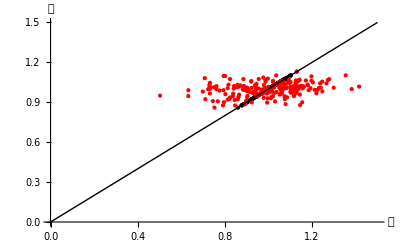

```mathematica
SetupForSims;
𝔊=1.00;
𝓅Std=ϑStd=0.05;
𝓅Group=𝓅Poor=1;
AddObsToPermLev:=AppendTo[𝓅,𝓅Group+RandomReal[NormalDistribution[0,𝓅Std]]];
Do[AddObs,{NObs}];
Print[FitLine=LinearModelFit[Transpose[{𝓎,𝒸}],{1,y},y]];FitPlot=Plot[FitLine,{y,Min[𝓎],Max[𝓎]},PlotStyle->Black];
Degree45=Plot[y,{y,0,1.5},PlotStyle->Black];
𝒸eq𝓅Color=Black;
𝒸eq𝓅Plot=ListPlot[Transpose[{𝓅,𝒸}],PlotStyle->𝒸eq𝓅Color];
𝓎PIHPlot=ListPlot[Transpose[{𝓎,𝓅}],PlotStyle->𝓎Color];
𝒸iVs𝓎iPlot=Show[𝒸eq𝓅Plot,𝓎PIHPlot,AxesLabel->{"𝓎","𝒸"}];
𝒸iVs𝓎iVsFitOneGroupPlot=Show[𝒸iVs𝓎iPlot,FitPlot,Degree45
,PlotRange->{{0,1.5},{0,1.5}}
,AxesOrigin->{0.,0.}
];
Print[ExportFigure[𝒸iVs𝓎iVsFitOneGroupPlot,"CiVsYiVsFitOneGroupPlotv3"]];
```

```mathematica
𝓅Group=𝓅Rich=1.2;Do[AddObs,{NObs}]; (* Now make a group with a higher permanent income *)
```

```mathematica
Print[LinearModelFit[Transpose[{𝓎,𝒸}],{1,y},y]];
```

FittedModel[0.724536+0.340696 y]

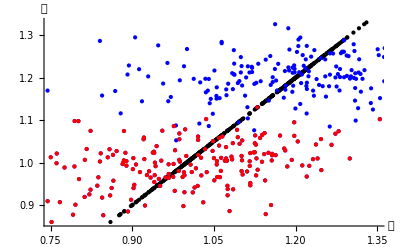

```mathematica
𝓎Color=Blue;
𝒸eq𝓅Plot=ListPlot[Transpose[{𝓅,𝒸}],PlotStyle->𝒸eq𝓅Color];
𝓎PIHPlot2=ListPlot[Transpose[{𝓎,𝒸}],PlotStyle->𝓎Color];
𝒸iVs𝓎iTwoGroupsPlot=Show[𝒸eq𝓅Plot,𝓎PIHPlot2,𝓎PIHPlot,AxesLabel->{"𝓎","𝒸"}
,PlotRange->{{1-5 ϑStd,𝓅Rich+3 ϑStd},Automatic}
,AxesOrigin->{1-5 ϑStd,Min[𝓎]}
];
Print[ExportFigure[𝒸iVs𝓎iTwoGroupsPlot,"CiVsYiTwoGroupsPlot"]];
```

```mathematica
𝓎𝒸All=Transpose[{𝓎,𝒸}];
𝒸Rich=Take[𝒸,-100];
𝓎Rich=Take[𝓎,-100];
𝓎𝒸Rich=Transpose[{𝓎Rich,𝒸Rich}];
𝒸Poor=Take[𝒸,100];
𝓎Poor=Take[𝓎,100];
𝓎𝒸Poor=Transpose[{𝓎Poor,𝒸Poor}];
𝒸MeanRich=Mean[𝒸Rich];
𝓎MeanRich=Mean[𝓎Rich];
𝒸MeanPoor=Mean[𝒸Poor];
𝓎MeanPoor=Mean[𝓎Poor];
𝒸ByGroup={𝒸MeanPoor,𝒸MeanRich};
𝓎ByGroup={𝓎MeanPoor,𝓎MeanRich};
```

```mathematica
Print[MatrixForm[𝓎𝒸Grouped=Transpose[{𝓎ByGroup,𝒸ByGroup}],TableHeadings->{{" Poor "," Rich "},{"   𝓎","   𝒸"}}]];
```

( |    𝓎 |    𝒸
 Poor  | 1.0052 | 1.00123
 Rich  | 1.19238 | 1.20233)

```mathematica
Print[Fit[𝓎𝒸Grouped,{1,y},y]];
```

-0.0787101+1.07435 y

```mathematica
Print[Fit[𝓎𝒸All,{1,y},y]];
```

0.724536+0.340696 y

```mathematica
Print[Fit[𝓎𝒸Rich,{1,y},y]];
```

1.16498+0.031317 y

```mathematica
Print[Fit[𝓎𝒸Poor,{1,y},y]];
```

0.923141+0.0776823 y